```mathematica
"Overall Model:"
ToExpression["C_{NO} = [init]_{nono} e^{-t/\tau_{nono}} - [init]_{no}e^{-t/\tau_{nono}}", TeXForm];
```

Overall Model:

ToExpression::esntx: Could not parse C_{NO} = [init]_{nono} e^{-t/	au_{nono}} - [init]_{no}e^{-t/	au_{nono}} as input.

```mathematica
(* Taunono and tauno are constants; change if nonoate type changes*)
(* Note that this works for all units as long as they are consistent*)
taunono = 107458; 
tauno = 641;
initnono = 500;
(*I thought this should be 0 by default, can be changed though*)
initno = 0;
```

```mathematica
Cno = (initnono*e^(-x/taunono)-initno*e^(-x/tauno))*e^(-x/tauno)
```

500 e^(-108099 x/68880578)

```mathematica
Plot[Cno, {x, 0, 1500}]
```

-Graphics-

1+x

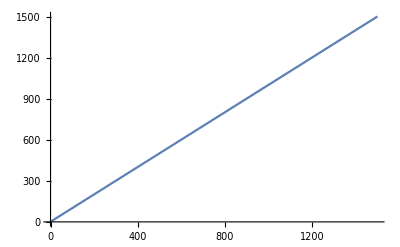

```mathematica
Cx = x+1
Plot[Cx, {x, 0, 1500}]
```